Harmonic Oscillator exact solution

```mathematica
ψexactHO[x_,n_]:=ψexactHO[x,n]=1/(√(2^n*Factorial[n]))*Pi^(-1/4) *E^(-x^2/2)*HermiteH[n,x]
```

Specific values for the HO: (a,b are the turning points)

```mathematica
En[n_]:=n+1/2
V[x_]:=x^2/2
derV[x_]:=x
a[n_]:=-√(2*En[n])
b[n_]:=-a[n]
```

Functions in the classically allowed zones,   x < 0 and x > 0, respectivelly:

```mathematica
ψa1[x_,n_]:=ψa1[x,n]=√((2Abs[derV[a[n]]])^(1/3)/(Pi*√(2*(En[n]-V[x]))))Cos[Integrate[√(2(En[n]-V[t])),{t,a[n],x},Assumptions->{n≥0,a[n]<x,x<0}]-Pi/4]
```

```mathematica
ψa2[x_,n_]:=ψa2[x,n]=√((2Abs[derV[a[n]]])^(1/3)/(Pi*√(2*(En[n]-V[x]))))Cos[Integrate[√(2(En[n]-V[t])),{t,x,b[n]},Assumptions->{n≥0,b[n]>x,x>0}]-Pi/4]
```

Functions in the classically forbidden zones,  x < a e x > b, respectivelly:

```mathematica
ψf1[x_,n_]:=ψf1[x,n]=√((2Abs[derV[a[n]]])^(1/3)/(Pi*√(2*(V[x]-En[n]))))*1/2 Exp[-Integrate[√(2(V[t]-En[n])),{t,x,a[n]},Assumptions->{n≥0,x<a[n]}]]
ψf2[x_,n_]:=ψf2[x,n]=√((2Abs[derV[a[n]]])^(1/3)/(Pi*√(2*(V[x]-En[n]))))*1/2 Exp[-Integrate[√(2(V[t]-En[n])),{t,b[n],x},Assumptions->{n≥0,x>b[n]}]]
```

Joining asymptotic solutions:

```mathematica
ψwkbasy[x_,n_]:=ψwkbasy[x,n]=(-1)^n ψf1[x,n](1-UnitStep[x-a[n]])+(-1)^n ψa1[x,n]UnitStep[x-a[n]](1-UnitStep[x])+ψa2[x,n]UnitStep[x](1-UnitStep[x-b[n]])+ψf2[x,n]UnitStep[x-b[n]]
```

Level N = 1

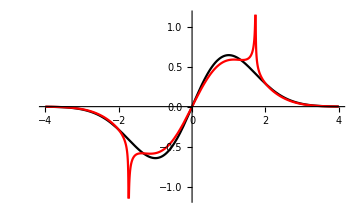

```mathematica
level=1
Plot[{ψexactHO[x,level],ψwkbasy[x,level]},{x,-4,4},GridLines->{{a[level],b[level]}},PlotStyle->{GrayLevel[0],Hue[0]},PlotRange->{-1.15,1.15}]
```

N=10

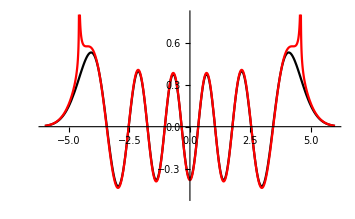

```mathematica
level=10
Plot[{ψexactHO[x,level],ψwkbasy[x,level]},{x,-6,6},GridLines->{{a[level],b[level]}},PlotStyle->{GrayLevel[0],Hue[0]},PlotRange->{-0.5,0.8}]
```

N=13

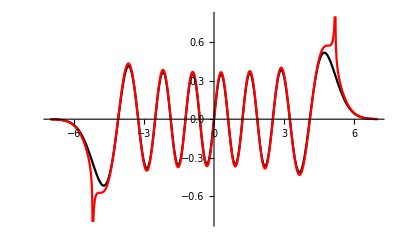

```mathematica
level=13
Plot[{ψexactHO[x,level],ψwkbasy[x,level]},{x,-7,7},GridLines->{{a[level],b[level]}},PlotStyle->{GrayLevel[0],Hue[0]},PlotRange->{-0.8,0.8}]
```

N=7

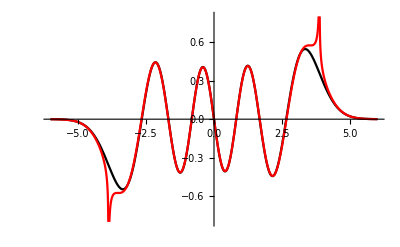

```mathematica
level=7
Plot[{ψexactHO[x,level],ψwkbasy[x,level]},{x,-6,6},GridLines->{{a[level],b[level]}},PlotStyle->{GrayLevel[0],Hue[0]},PlotRange->{-0.8,0.8}]
```

As one would expect, near the turning points,  p1 or p2 → 0 and the WKB solution goes to infinity. The higher the value of N and subsequently the higher the energy value, the better the semi-classical aproximation and the better the overlap betwwen exact soluton and approximate, in the allowed region.